Clear::ssym: q1 ， q2 ， q3 is not a symbol or a string.

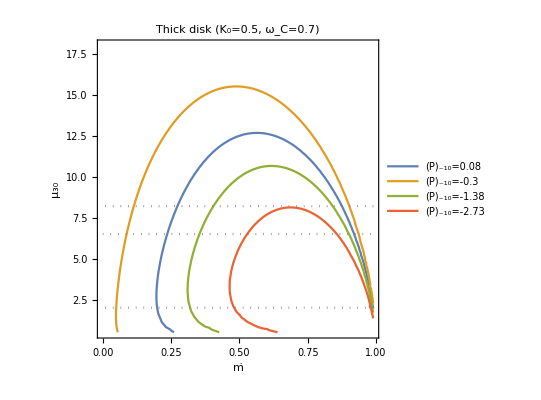

```mathematica
(*
Thick disk model/Reference model
Subscript[K, 0]=0.5,Subscript[ω, C]=0.7
N/(Subscript[N, 0]')=f(Subscript[ω, s]')
(-4/5 πMR^2 P^2 Ṗ)/(2^(-1/14)Subscript[K, 0]^(1/2)(GM)^(3/7)u^(2/7)A^(-1/7)(Ṁ)^(6/7))=1-1/Subscript[Aω, C]*2^(11/14)Subscript[πK, 0]^(3/2)(GM)^(-5/7)P^-1(Ṁ)^(-3/7)μ^(6/7)
*)
Clear[w,k,G,M,R,P,u,MEdd,a,b,q1，q2，q3,q4,x,A,fig1,equ]
w=0.7;
k=0.5;
G=6.67*10^-8;
M=2.8*10^33;
(*M=1.4 M_⊙*)
R=10^6;
P=1.37;
q1=-1.2;
q2=-0.3;
q3=-1.87;
q4=-2.73;
(*q=Subscript[Ṗ, -10]={0.08,-0.3,-1.38,-2.73}*)
(*u=25;*)
(*μ=1/2 BR^3,B=5*10^13 G*)
MEdd=10^20;
a=1/w*k^(3/2)*(G*M)^(-5/7)*P^-1*(MEdd)^(-3/7)*2.80517*10^26;
(*a=1/Subscript[ω, C]*2^(11/14)Subscript[πK, 0]^(3/2)(GM)^(-5/7)P^-1 Subscript[Ṁ, E]^(-3/7)
=1/Subscript[ω, C]*2^(11/14)Subscript[πK, 0]^(3/2)(GM)^(-5/7)P^-1 Subscript[Ṁ, E]^(-3/7)*(10^30)^(6/7)
2.^(11/14)*Pi*(10^30)^(6/7)=2.80517*10^26*)
b=(M*R^2*P^2)/(k^(1/2)*(G*M)^(3/7)*(MEdd)^(6/7))*(-7.08457*10^-19);
(*b=(-4/5 πMR^2 P^2)/(2^(-1/14)Subscript[K, 0]^(1/2)(GM)^(3/7)Subscript[Ṁ, E]^(6/7))
=(-4/5 πMR^2 P^2*10^-10)/(2^(-1/14)Subscript[K, 0]^(1/2)(GM)^(3/7)Subscript[Ṁ, E]^(6/7)*(10^30)^(2/7))
(-4/5*Pi*10^-10)/(2.^(-1/14)*(10^30)^(2/7))=-7.08457*10^-19*)
equ=(1-x)^(-1/14)x^(6/7)u^(2/7)-a(1-x)^(-4/7)x^(3/7)u^(8/7);
b*q1;
b*q2;
b*q3;
b*q4;
(*
x=ṁ
Ṗ 和 ṁ 的关系
(b Subscript[Ṗ, -10])/(A^(-1/7)(ṁ)^(6/7)Subscript[μ, 30]^(2/7))=1-a(ṁ)^(-3/7)Subscript[μ, 30]^(6/7)
Subscript[Ṗ, -10]=(((ṁ)^(3/7)-a)(ṁ)^(3/7))/(b(1-ṁ)^(4/7)) (*A=(1-ṁ)^(1/2)*)
*)
fig1=ContourPlot[
{(1-x)^(-1/14)*x^(6/7)*u^(2/7)-a*(1-x)^(-4/7)*x^(3/7)*u^(8/7)-b*q1==0,
(1-x)^(-1/14)*x^(6/7)*u^(2/7)-a*(1-x)^(-4/7)*x^(3/7)*u^(8/7)-b*q2==0,
(1-x)^(-1/14)*x^(6/7)*u^(2/7)-a*(1-x)^(-4/7)*x^(3/7)*u^(8/7)-b*q3==0,
(1-x)^(-1/14)*x^(6/7)*u^(2/7)-a*(1-x)^(-4/7)*x^(3/7)*u^(8/7)-b*q4==0,
u-6.5==0,
u-8.2==0,
u-2==0},
{x,0,0.99},{u,0.5,18},
PlotLabel->"Thick disk (K_0=0.5, ω_C=0.7)",
PlotLegends->{"(Ṗ)_-10=0.08","(Ṗ)_-10=-0.3","(Ṗ)_-10=-1.38","(Ṗ)_-10=-2.73"},
FrameLabel->{"ṁ","μ_30"},
ContourStyle->{,,,,{Gray,Dotted},{Gray,Dotted},{Gray,Dotted}}]
(*fig2=ContourPlot[{(1-x)^(-1/14)*x^(6/7)*u^(2/7)-a*(1-x)^(-4/7)*x^(3/7)*u^(8/7)-b*q1==0,(1-x)^(-1/14)*x^(6/7)*u^(2/7)-a*(1-x)^(-4/7)*x^(3/7)*u^(8/7)-b*q2==0,(1-x)^(-1/14)*x^(6/7)*u^(2/7)-a*(1-x)^(-4/7)*x^(3/7)*u^(8/7)-b*q3==0,(1-x)^(-1/14)*x^(6/7)*u^(2/7)-a*(1-x)^(-4/7)*x^(3/7)*u^(8/7)-b*q4==0},{x,0,0.99},{u,0.5,9},(*PlotLabel->"Thick disk((Ṁ)_E=10^20)",PlotLegends->{"(Ṗ)_-10=0.08","(Ṗ)_-10=-0.3","(Ṗ)_-10=-1.38","(Ṗ)_-10=-2.73"},*)FrameLabel->{"ṁ","μ_30"}]
(*(1-x)^(-1/14)x^(6/7)u^(2/7)-a(1-x)^(-4/7)x^(3/7)u^(8/7)-b*q==0,去掉b*q，即(1-x)^(-1/14)x^(6/7)u^(2/7)-a(1-x)^(-4/7)x^(3/7)u^(8/7)==b*q的康拓图*)
*)
```

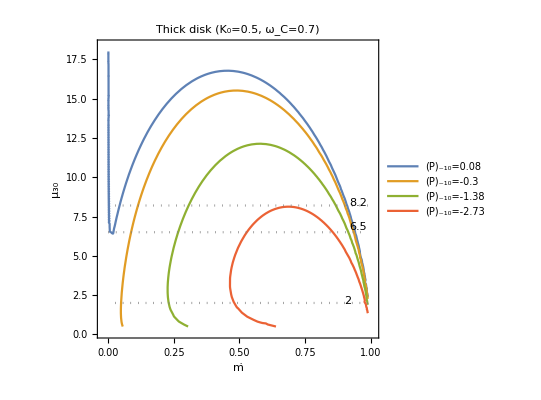

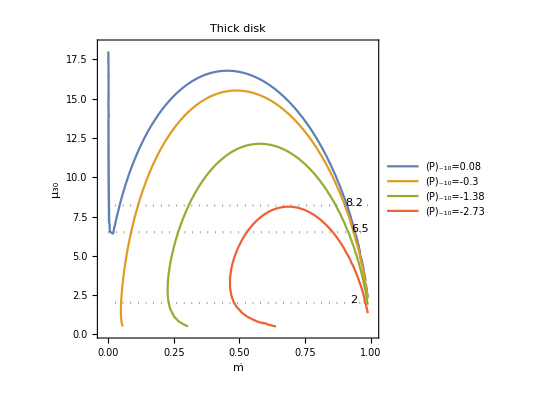

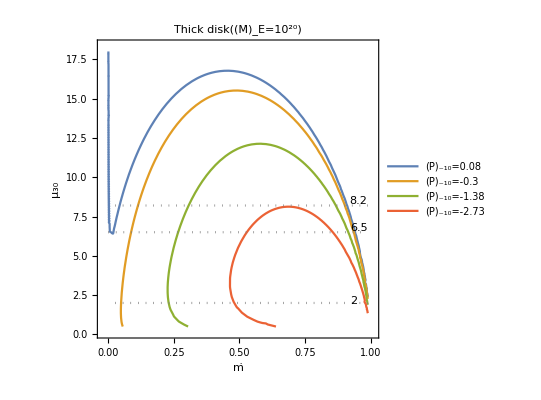

```mathematica
(*(*u=4*)
u=4.0;
equ=-(0.047639177278886585 u^(8/7) x^(3/7))/(1-x)^(4/7)+(u^(2/7) x^(6/7))/(1-x)^(1/14)*)
```

-(0.232291 x^(3/7))/(1-x)^(4/7)+(1.48599 x^(6/7))/(1-x)^(1/14)

```mathematica
(*(*u=4*)
(*0.08*)FindRoot[equ==b*q1,{x,0.9}]
(*-0.3*)FindRoot[equ==b*q2,{x,0.9}]
(*-1.38*)FindRoot[equ==b*q3,{x,0.9}]
(*-2.73*)FindRoot[equ==b*q4,{x,0.9}]*)
```

{x→0.975472}

{x→0.973237}

{x→0.964492}

{x→0.943008}

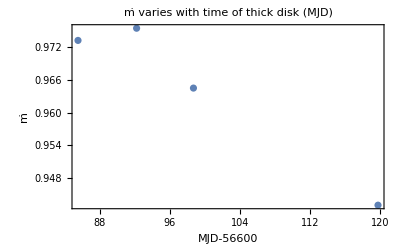

```mathematica
(*ListPlot[{{85.5,0.973237},{92.2,0.975472},{98.7,0.964492},{119.8,0.943008}},FrameLabel->{"MJD-56600","ṁ"},Frame->True,PlotLabel->"ṁ varies with time of thick disk (MJD)"]
(*ListPlot[{{6,0.973237},{7,0.975472},{8,0.964492},{11,0.943008}},AxesLabel->{"obsID","ṁ"},PlotLabel->"ṁ varies with time of thick disk (obsID)"]*)*)
```

```mathematica
(*(*u=8*)
Clear[u,x]
u=8.0;
(*0.08*)FindRoot[equ==b*q1,{x,0.9}]
(*-0.3*)FindRoot[equ==b*q2,{x,0.9}]
(*-1.38*)FindRoot[equ==b*q3,{x,0.9}]
(*-2.73*)FindRoot[equ==b*q4,{x,0.9}]*)
```

{x→0.91489}

{x→0.907018}

{x→0.874367}

{x→0.73482}

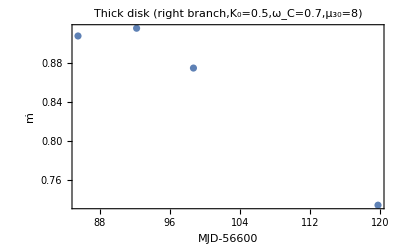

```mathematica
(*ListPlot[{{85.5,0.907018},{92.2,0.91489},{98.7,0.874367},{119.8,0.73482}},FrameLabel->{"MJD-56600","ṁ"},Frame->True,PlotLabel->"Thick disk (right branch,K_0=0.5,ω_C=0.7,μ_30=8)"]*)
```

```mathematica
(*(*u=2*)
Clear[u,x]
u=2.0;
(*0.08*)FindRoot[equ==b*q1,{x,0.9}]
(*-0.3*)FindRoot[equ==b*q2,{x,0.9}]
(*-1.38*)FindRoot[equ==b*q3,{x,0.9}]
(*-2.73*)FindRoot[equ==b*q4,{x,0.9}]*)
```

{x→0.992649}

{x→0.99192}

{x→0.989014}

{x→0.981717}

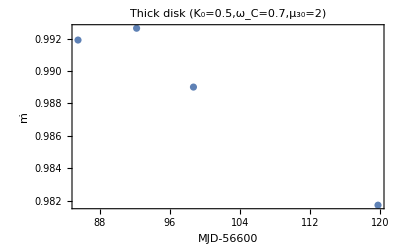

```mathematica
(*ListPlot[{{85.5,0.99192},{92.2,0.992649},{98.7,0.989014},{119.8,0.981717}},FrameLabel->{"MJD-56600","ṁ"},Frame->True,PlotLabel->"Thick disk (K_0=0.5,ω_C=0.7,μ_30=2)"]*)
```

```mathematica
(*(*u=8,不能解释观测*)
Clear[u,x]
u=8.0;
(*0.08*)FindRoot[equ==b*q1,{x,0.1}]
(*-0.3*)FindRoot[equ==b*q2,{x,0.1}]
(*-1.38*)FindRoot[equ==b*q3,{x,0.3}]
(*-2.73*)FindRoot[equ==b*q4,{x,0.5}]*)
```

{x→0.0403722}

{x→0.110067}

{x→0.301145}

{x→0.639973}

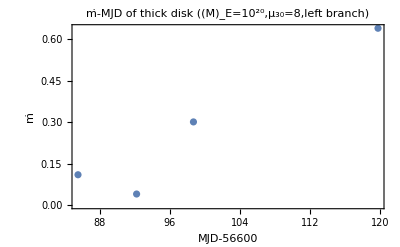

```mathematica
(*ListPlot[{{85.5,0.110067},{92.2,0.0403722},{98.7,0.301145},{119.8,0.639973}},FrameLabel->{"MJD-56600","ṁ"},Frame->True,PlotLabel->"ṁ-MJD of thick disk ((Ṁ)_E=10^20,μ_30=8,left branch)"]*)
```

```mathematica
(*结论：thick disk模型,对应的u=2-8,磁场为(4-16)*10^12 G,都可以解释观测*)
```

Clear::ssym: q1 ， q2 ， q3 is not a symbol or a string.

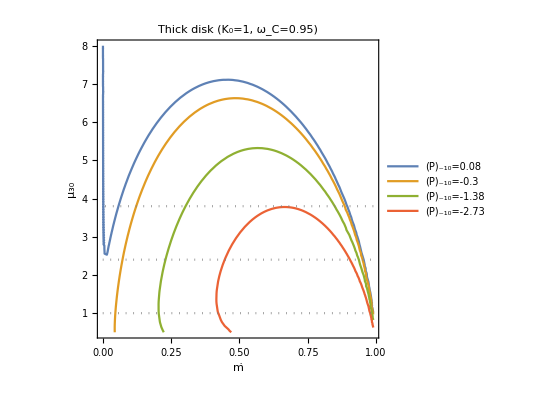

```mathematica
(*(*
Thick disk model/Reference model
Subscript[K, 0]=1,Subscript[ω, C]=0.95
N/(Subscript[N, 0]')=f(Subscript[ω, s]')
(-4/5 πMR^2 P^2 Ṗ)/(2^(-1/14)Subscript[K, 0]^(1/2)(GM)^(3/7)u^(2/7)A^(-1/7)(Ṁ)^(6/7))=1-1/Subscript[Aω, C]*2^(11/14)Subscript[πK, 0]^(3/2)(GM)^(-5/7)P^-1(Ṁ)^(-3/7)μ^(6/7)
*)
Clear[w,k,G,M,R,P,u,MEdd,a,b,q1，q2，q3,q4,x,A,fig1,equ]
w=0.95;
k=1;
G=6.67*10^-8;
M=2.8*10^33;
(*M=1.4 M_⊙*)
R=10^6;
P=1.37;
q1=0.08;
q2=-0.3;
q3=-1.38;
q4=-2.73;
(*q=Subscript[Ṗ, -10]={0.08,-0.3,-1.38,-2.73}*)
(*u=25;*)
(*μ=1/2 BR^3,B=5*10^13 G*)
MEdd=10^20;
a=1/w*k^(3/2)*(G*M)^(-5/7)*P^-1*(MEdd)^(-3/7)*2.80517*10^26;
(*a=1/Subscript[ω, C]*2^(11/14)Subscript[πK, 0]^(3/2)(GM)^(-5/7)P^-1 Subscript[Ṁ, E]^(-3/7)
=1/Subscript[ω, C]*2^(11/14)Subscript[πK, 0]^(3/2)(GM)^(-5/7)P^-1 Subscript[Ṁ, E]^(-3/7)*(10^30)^(6/7)
2.^(11/14)*Pi*(10^30)^(6/7)=2.80517*10^26*)
b=(M*R^2*P^2)/(k^(1/2)*(G*M)^(3/7)*(MEdd)^(6/7))*(-7.08457*10^-19);
(*b=(-4/5 πMR^2 P^2)/(2^(-1/14)Subscript[K, 0]^(1/2)(GM)^(3/7)Subscript[Ṁ, E]^(6/7))
=(-4/5 πMR^2 P^2*10^-10)/(2^(-1/14)Subscript[K, 0]^(1/2)(GM)^(3/7)Subscript[Ṁ, E]^(6/7)*(10^30)^(2/7))
(-4/5*Pi*10^-10)/(2.^(-1/14)*(10^30)^(2/7))=-7.08457*10^-19*)
equ=(1-x)^(-1/14)x^(6/7)u^(2/7)-a(1-x)^(-4/7)x^(3/7)u^(8/7);
b*q1;
b*q2;
b*q3;
b*q4;
(*
x=ṁ right branch,Subscript[K, 0]=0.5,Subscript[ω, C]=0.7,Subscript[μ, 30]=2
Ṗ 和 ṁ 的关系
(b Subscript[Ṗ, -10])/(A^(-1/7)(ṁ)^(6/7)Subscript[μ, 30]^(2/7))=1-a(ṁ)^(-3/7)Subscript[μ, 30]^(6/7)
Subscript[Ṗ, -10]=(((ṁ)^(3/7)-a)(ṁ)^(3/7))/(b(1-ṁ)^(4/7)) (*A=(1-ṁ)^(1/2)*)
*)
fig1=ContourPlot[
{(1-x)^(-1/14)*x^(6/7)*u^(2/7)-a*(1-x)^(-4/7)*x^(3/7)*u^(8/7)-b*q1==0,
(1-x)^(-1/14)*x^(6/7)*u^(2/7)-a*(1-x)^(-4/7)*x^(3/7)*u^(8/7)-b*q2==0,
(1-x)^(-1/14)*x^(6/7)*u^(2/7)-a*(1-x)^(-4/7)*x^(3/7)*u^(8/7)-b*q3==0,
(1-x)^(-1/14)*x^(6/7)*u^(2/7)-a*(1-x)^(-4/7)*x^(3/7)*u^(8/7)-b*q4==0,
u-1==0,
u-3.8==0,
u-2.4==0},
{x,0,0.99},{u,0.5,8},
PlotLabel->"Thick disk (K_0=1, ω_C=0.95)",
PlotLegends->{"(Ṗ)_-10=0.08","(Ṗ)_-10=-0.3","(Ṗ)_-10=-1.38","(Ṗ)_-10=-2.73"},
FrameLabel->{"ṁ","μ_30"},
ContourStyle->{,,,,{Gray,Dotted},{Gray,Dotted},{Gray,Dotted}}]
(*fig2=ContourPlot[{(1-x)^(-1/14)*x^(6/7)*u^(2/7)-a*(1-x)^(-4/7)*x^(3/7)*u^(8/7)-b*q1==0,(1-x)^(-1/14)*x^(6/7)*u^(2/7)-a*(1-x)^(-4/7)*x^(3/7)*u^(8/7)-b*q2==0,(1-x)^(-1/14)*x^(6/7)*u^(2/7)-a*(1-x)^(-4/7)*x^(3/7)*u^(8/7)-b*q3==0,(1-x)^(-1/14)*x^(6/7)*u^(2/7)-a*(1-x)^(-4/7)*x^(3/7)*u^(8/7)-b*q4==0},{x,0,0.99},{u,0.5,9},(*PlotLabel->"Thick disk((Ṁ)_E=10^20)",PlotLegends->{"(Ṗ)_-10=0.08","(Ṗ)_-10=-0.3","(Ṗ)_-10=-1.38","(Ṗ)_-10=-2.73"},*)FrameLabel->{"ṁ","μ_30"}]
(*(1-x)^(-1/14)x^(6/7)u^(2/7)-a(1-x)^(-4/7)x^(3/7)u^(8/7)-b*q==0,去掉b*q，即(1-x)^(-1/14)x^(6/7)u^(2/7)-a(1-x)^(-4/7)x^(3/7)u^(8/7)==b*q的康拓图*)
*)right branch,Subscript[K, 0]=0.5,Subscript[ω, C]=0.7,Subscript[μ, 30]=2*)
```

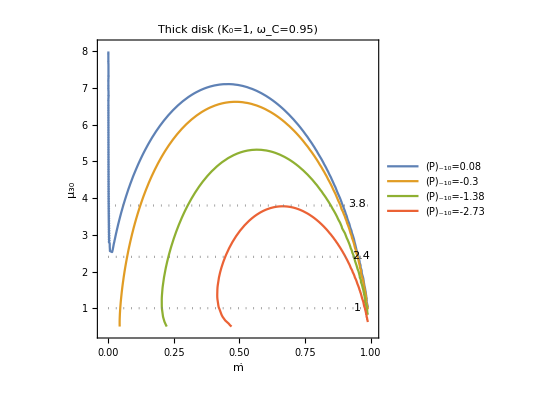

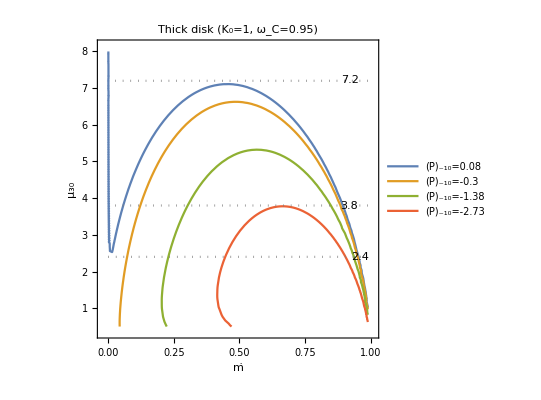

```mathematica
(*(*u=2*)
Clear[u,x]
u=2.0;
(*0.08*)FindRoot[equ==b*q1,{x,0.9}]
(*-0.3*)FindRoot[equ==b*q2,{x,0.9}]
(*-1.38*)FindRoot[equ==b*q3,{x,0.9}]
(*-2.73*)FindRoot[equ==b*q4,{x,0.9}]*)
```

{x→0.967231}

{x→0.96458}

{x→0.954551}

{x→0.931885}

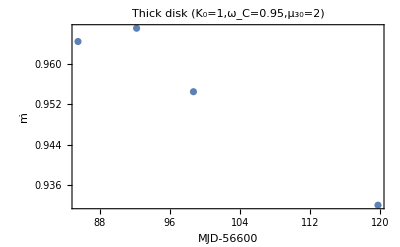

```mathematica
(*ListPlot[{{85.5,0.96458},{92.2,0.967231},{98.7,0.954551},{119.8,0.931885}},FrameLabel->{"MJD-56600","ṁ"},Frame->True,PlotLabel->"Thick disk (K_0=1,ω_C=0.95,μ_30=2)"]*)
```

```mathematica
(*(*u=3*)
Clear[u,x]
u=3.0;
(*0.08*)FindRoot[equ==b*q1,{x,0.9}]
(*-0.3*)FindRoot[equ==b*q2,{x,0.9}]
(*-1.38*)FindRoot[equ==b*q3,{x,0.9}]
(*-2.73*)FindRoot[equ==b*q4,{x,0.9}]*)
```

{x→0.932191}

{x→0.92667}

{x→0.905235}

{x→0.849884}

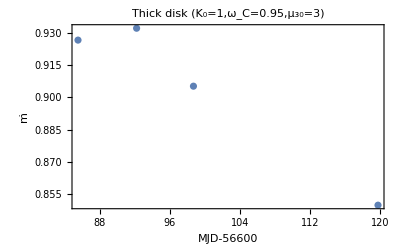

```mathematica
(*ListPlot[{{85.5,0.92667},{92.2,0.932191},{98.7,0.905235},{119.8,0.849884}},FrameLabel->{"MJD-56600","ṁ"},Frame->True,PlotLabel->"Thick disk (K_0=1,ω_C=0.95,μ_30=3)"]*)
```

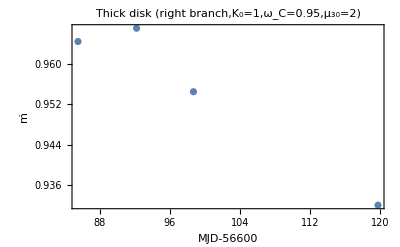
```mathematica
(*(*
Thick disk model/Reference model
Subscript[K, 0]=1,Subscript[ω, C]=0.95
N/(Subscript[N, 0]')=f(Subscript[ω, s]')
(-4/5 πMR^2 P^2 Ṗ)/(2^(-1/14)Subscript[K, 0]^(1/2)(GM)^(3/7)u^(2/7)A^(-1/7)(Ṁ)^(6/7))=1-1/Subscript[Aω, C]*2^(11/14)Subscript[πK, 0]^(3/2)(GM)^(-5/7)P^-1(Ṁ)^(-3/7)μ^(6/7)
*)
Clear[w,k,G,M,R,P,u,MEdd,a,b,q1，q2，q3,q4,x,A,fig1,equ]
w=0.95;
k=0.5;
G=6.67*10^-8;
M=2.8*10^33;
(*M=1.4 M_⊙*)
R=10^6;
P=1.37;
q1=0.08;
q2=-0.3;
q3=-1.38;
q4=-2.73;
(*q=Subscript[Ṗ, -10]={0.08,-0.3,-1.38,-2.73}*)
(*u=25;*)
(*μ=1/2 BR^3,B=5*10^13 G*)
MEdd=10^20;
a=1/w*k^(3/2)*(G*M)^(-5/7)*P^-1*(MEdd)^(-3/7)*2.80517*10^26;
(*a=1/Subscript[ω, C]*2^(11/14)Subscript[πK, 0]^(3/2)(GM)^(-5/7)P^-1 Subscript[Ṁ, E]^(-3/7)
=1/Subscript[ω, C]*2^(11/14)Subscript[πK, 0]^(3/2)(GM)^(-5/7)P^-1 Subscript[Ṁ, E]^(-3/7)*(10^30)^(6/7)
2.^(11/14)*Pi*(10^30)^(6/7)=2.80517*10^26*)
b=(M*R^2*P^2)/(k^(1/2)*(G*M)^(3/7)*(MEdd)^(6/7))*(-7.08457*10^-19);
(*b=(-4/5 πMR^2 P^2)/(2^(-1/14)Subscript[K, 0]^(1/2)(GM)^(3/7)Subscript[Ṁ, E]^(6/7))
=(-4/5 πMR^2 P^2*10^-10)/(2^(-1/14)Subscript[K, 0]^(1/2)(GM)^(3/7)Subscript[Ṁ, E]^(6/7)*(10^30)^(2/7))
(-4/5*Pi*10^-10)/(2.^(-1/14)*(10^30)^(2/7))=-7.08457*10^-19*)
equ=(1-x)^(-1/14)x^(6/7)u^(2/7)-a(1-x)^(-4/7)x^(3/7)u^(8/7);
b*q1;
b*q2;
b*q3;
b*q4;
(*
x=ṁ
Ṗ 和 ṁ 的关系
(b Subscript[Ṗ, -10])/(A^(-1/7)(ṁ)^(6/7)Subscript[μ, 30]^(2/7))=1-a(ṁ)^(-3/7)Subscript[μ, 30]^(6/7)
Subscript[Ṗ, -10]=(((ṁ)^(3/7)-a)(ṁ)^(3/7))/(b(1-ṁ)^(4/7)) (*A=(1-ṁ)^(1/2)*)
*)
fig1=ContourPlot[
{(1-x)^(-1/14)*x^(6/7)*u^(2/7)-a*(1-x)^(-4/7)*x^(3/7)*u^(8/7)-b*q1==0,
(1-x)^(-1/14)*x^(6/7)*u^(2/7)-a*(1-x)^(-4/7)*x^(3/7)*u^(8/7)-b*q2==0,
(1-x)^(-1/14)*x^(6/7)*u^(2/7)-a*(1-x)^(-4/7)*x^(3/7)*u^(8/7)-b*q3==0,
(1-x)^(-1/14)*x^(6/7)*u^(2/7)-a*(1-x)^(-4/7)*x^(3/7)*u^(8/7)-b*q4==0,
u-7.2==0,
u-3.8==0,
u-2.4==0},
{x,0,0.99},{u,0.5,15},
PlotLabel->"Thick disk (K_0=1, ω_C=0.95)",
PlotLegends->{"(Ṗ)_-10=0.08","(Ṗ)_-10=-0.3","(Ṗ)_-10=-1.38","(Ṗ)_-10=-2.73"},
FrameLabel->{"ṁ","μ_30"},
ContourStyle->{,,,,{Gray,Dotted},{Gray,Dotted},{Gray,Dotted}}]
(*fig2=ContourPlot[{(1-x)^(-1/14)*x^(6/7)*u^(2/7)-a*(1-x)^(-4/7)*x^(3/7)*u^(8/7)-b*q-Graphics-1==0,(1-x)^(-1/14)*x^(6/7)*u^(2/7)-a*(1-x)^(-4/7)*x^(3/7)*u^(8/7)-b*q2==0,(1-x)^(-1/14)*x^(6/7)*u^(2/7)-a*(1-x)^(-4/7)*x^(3/7)*u^(8/7)-b*q3==0,(1-x)^(-1/14)*x^(6/7)*u^(2/7)-a*(1-x)^(-4/7)*x^(3/7)*u^(8/7)-b*q4==0},{x,0,0.99},{u,0.5,9},(*PlotLabel->"Thick disk((Ṁ)_E=10^20)",PlotLegends->{"(Ṗ)_-10=0.08","(Ṗ)_-10=-0.3","(Ṗ)_-10=-1.38","(Ṗ)_-10=-2.73"},*)FrameLabel->{"ṁ","μ_30"}]
(*(1-x)^(-1/14)x^(6/7)u^(2/7)-a(1-x)^(-4/7)x^(3/7)u^(8/7)-b*q==0,去掉b*q，即(1-x)^(-1/14)x^(6/7)u^(2/7)-a(1-x)^(-4/7)x^(3/7)u^(8/7)==b*q的康拓图*)
*)*)
```

Clear::ssym: q1 ， q2 ， q3 is not a symbol or a string.